```mathematica
parsϕ = Delete[parsCoexH,Position[Keys[parsCoexH],ϕ]];
equilpar=equil/.parsϕ;
Jeq=J/.equil/.parsϕ//Simplify;
domEigs=Max/@Re/@Eigenvalues/@Jeq;
```

```mathematica
IsStable[ϕ_]:=Thread[domEigs<0]/.eP-> 0//Evaluate

temp=Table[
Plot[
{
R/.equilpar[[i]],
Ν/.equilpar[[i]],
P/.equilpar[[i]],
eΝ/.equilpar[[i]],
eP/.equilpar[[i]]
},
{ϕ,0,1},
RegionFunction->Function[ϕ,Evaluate[IsStable[ϕ][[i]]] ],
PlotRange->{{0,1},{0,3}},
PlotStyle-> {
{Thickness[0.015], Green},
{Thickness[0.015], Blue},
{Thickness[0.015], Red},
{Thickness[0.0075],Blue, Dashed},
{Thickness[0.0075],Red, Dashed}},
ScalingFunctions->{"Reverse",Identity}
],
{i,10,15}];
```

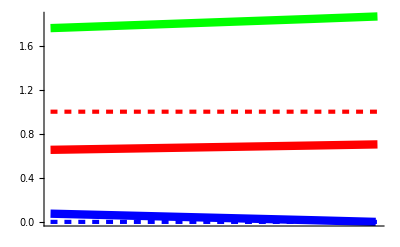
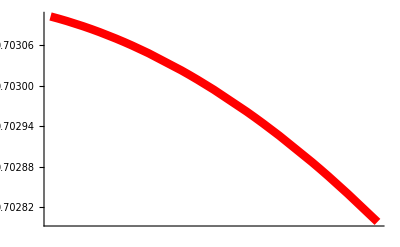
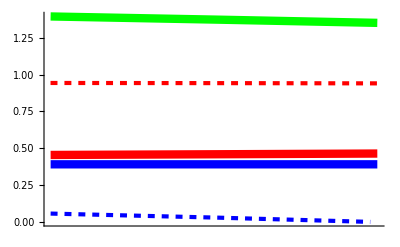
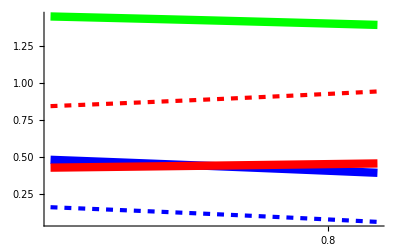
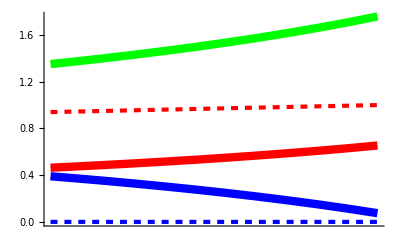
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
temp
```

```mathematica
Dimensions[equil][[1]]
```

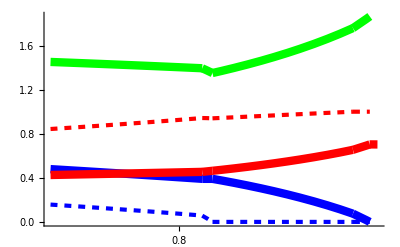

```mathematica
Show[temp]
```

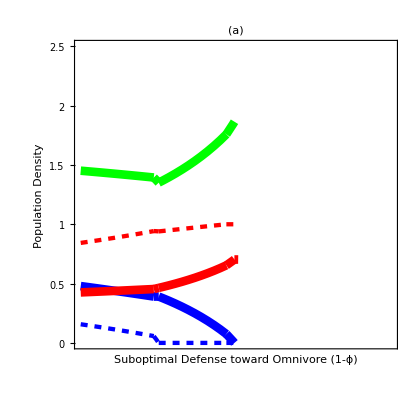

```mathematica
Show[temp,
Frame-> True,
FrameLabel->{"Suboptimal Defense toward Omnivore (1-ϕ)","Population Density", None,"Defense Effort"}, PlotLabel -> Style["(a)                                                                                       ", FontSize->14,  Bold],
ImageSize -> 414,Spacings-> 30, 
PlotRange-> {{-1,0},{0,2.5}},
AspectRatio -> 1/1, LabelStyle-> {Black, Larger}, 
FrameTicks->{
{{0,0.5,1, 1.5, 2, 2.5},{0,0.5,1, 1.5, 2, 2.5}},
{None, {None}}}]
```